## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
results={};
n=16;
primes=nprimes[n][[;;10000]];
```

## Prime 16

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
```

## Visibility Graph

```mathematica
natLinks16 =naturalVisibility[series];
```

## Graph

```mathematica
igv16=Graph[natLinks16, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv16];
```

```mathematica
count = Total[adj]//Counts
```

<|3→1863,5→1329,8→451,9→358,39→5,17→73,2→1241,7→624,4→1673,12→185,10→296,25→16,6→899,15→76,11→195,20→40,23→33,14→121,30→10,13→123,46→3,57→1,32→7,72→2,121→1,16→83,19→42,21→34,24→13,22→29,42→5,27→7,26→22,40→2,44→1,31→8,18→54,28→13,36→6,45→3,35→4,67→2,29→10,33→6,38→6,64→1,37→7,54→1,63→1,56→2,51→2,59→2,68→1,48→1,34→2,43→1,50→1,47→1,41→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{3,207/1111},{5,443/3333},{8,41/909},{9,358/9999},{39,5/9999},{17,73/9999},{2,1241/9999},{7,208/3333},{4,1673/9999},{12,185/9999},{10,296/9999},{25,16/9999},{6,899/9999},{15,76/9999},{11,65/3333},{20,40/9999},{23,1/303},{14,11/909},{30,10/9999},{13,41/3333},{46,1/3333},{57,1/9999},{32,7/9999},{72,2/9999},{121,1/9999},{16,83/9999},{19,14/3333},{21,34/9999},{24,13/9999},{22,29/9999},{42,5/9999},{27,7/9999},{26,2/909},{40,2/9999},{44,1/9999},{31,8/9999},{18,6/1111},{28,13/9999},{36,2/3333},{45,1/3333},{35,4/9999},{67,2/9999},{29,10/9999},{33,2/3333},{38,2/3333},{64,1/9999},{37,7/9999},{54,1/9999},{63,1/9999},{56,2/9999},{51,2/9999},{59,2/9999},{68,1/9999},{48,1/9999},{34,2/9999},{43,1/9999},{50,1/9999},{47,1/9999},{41,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.419408/x^1.077]

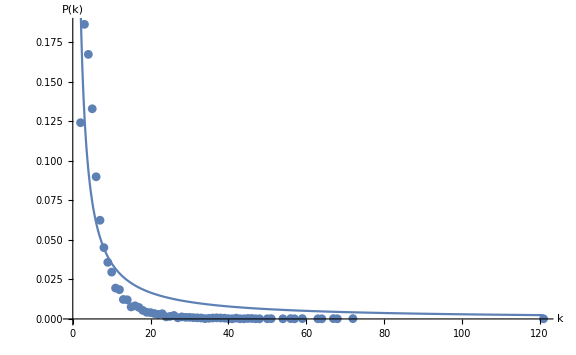

```mathematica
vis16=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis16];
```

## Mean degree

```mathematica
degree=VertexDegree[igv16]//Mean//N
```

6.30903

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks16=horizontalVisibility[series];
```

## Graph

```mathematica
igh16=Graph[horLinks16, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh16];
```

```mathematica
count = Total[adj]//Counts
```

<|2→3723,3→2239,7→402,6→571,4→1431,9→150,8→268,12→44,11→62,5→920,10→112,15→15,20→3,18→5,14→16,13→24,16→8,21→3,17→1,19→2|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,1241/3333},{3,2239/9999},{7,134/3333},{6,571/9999},{4,159/1111},{9,50/3333},{8,268/9999},{12,4/909},{11,62/9999},{5,920/9999},{10,112/9999},{15,5/3333},{20,1/3333},{18,5/9999},{14,16/9999},{13,8/3333},{16,8/9999},{21,1/3333},{17,1/9999},{19,2/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.27275/x^1.71034]

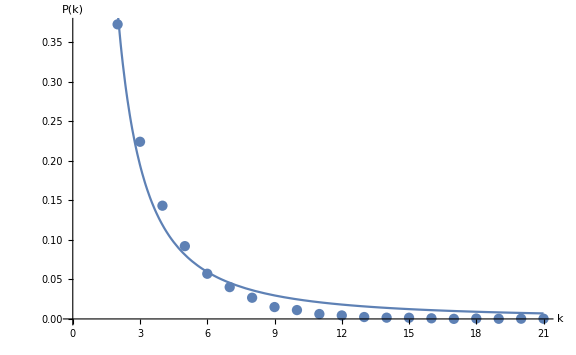

```mathematica
hvis16=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis16];
```

## Mean degree

```mathematica
degree=VertexDegree[igh16]//Mean//N
```

3.77118

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,13,9999,6.30903,1.077 ± 0.186338,0.419408 ± 0.113956},{horizontal,13,9999,3.77118,1.71034 ± 0.174246,1.27275 ± 0.215431}}